# The basics of 2D graphics

Math 250 - Math with Mathematica
Christopher Hanusa

## 8.1. Overview

In this tutorial, we work to understand and display two-dimensional graphics objects in Mathematica.

## 8.2. Graphics objects

### Syntax

When you are constructing graphics, you build them piece by piece by creating a list of Graphics primitives.  (A primitive is a basic building block.)  When you want to display these pieces together, wrap the list in a Graphics command.  This will generate a visual representation of your primitives in layers from bottom to top.

### Modifying primitives

There are many many properties, settings, and options available for Graphics objects. We’ll discuss some of them below. 
You may ask: “Can I make my object look like _______ ?” 
My answer: “Probably!”
The Documentation Center is your friend!

### Geometry

To make your graphics, it will take quite a bit of thinking and strategizing.  The most important thing to understand is that we will be placing 2D (and later 3D) objects using Cartesian coordinates.  [Think: (x,y) in 2D or (x,y,z) in 3D.]  You will need to plan out the positions of all the points.  This may involve trigonometry, for instance, to find the placement of a point on a circle.

### Show

If you have multiple graphics that you’d like to combine together, use the Show command to display them all at the same time.  The most important aspect of the Show command is that the combined object inherits the settings of the first graphic.  
You can also use the PlotRange -> All option, discussed below.

## 8.3. 0D objects: Points

A point is a zero-dimensional object; generate one using the Point command.
Remember that all graphics primitives need to be included in a Graphics command to be displayed.

```mathematica
Point[{0,0}]
```

Point[{0,0}]

```mathematica
Graphics[Point[{0,0}]]
```

-Graphics-

Graphics only takes as an input ONE object, so when you have more than one primitive to display, put them in a list.

```mathematica
Graphics[Point[{0,0}],Point[{1,1}]]
```

```mathematica
Graphics[{Point[{0,0}],Point[{1,1}]}]
```

-Graphics-

The Map command will come in handy.
Here we use Map to apply Point to many coordinate pairs.

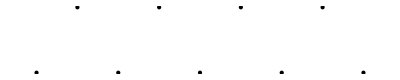

```mathematica
pointlist={{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}};
Graphics[Map[Point,pointlist]]
```

Do Now: Navigate to the Documentation Center entry for Point, and look at the “Neat Examples” at the bottom.

## 8.4. Color

Certain colors are predefined in Mathematica like Red, Orange, Yellow, etc.  
Furthermore, you can create any color using, among others, Hue and RGBColor.  
And you make colors lighter and darker using Lighter and Darker.
You can see the colors that are predefined in guide/Colors.

You change color by putting the color’s name before the primitive.

```mathematica
Graphics[{Red,Point[{0,0}]}]
```

-Graphics-

I suggest using braces to delimit where the color applies.  
Here I have also included the directive PointSize, which specifies the size of the point.
It is outside all the braces, so it applies to all subsequent primitives.

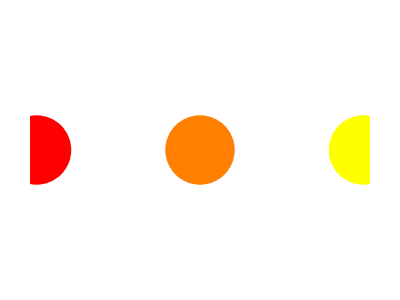

```mathematica
Graphics[{PointSize[.2],
{Red,Point[{0,0}]},
{Orange,Point[{1,0}]},
{Yellow,Point[{2,0}]}
}]
```

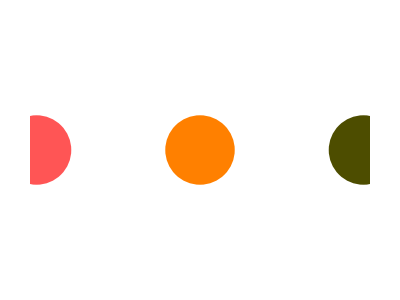

```mathematica
Graphics[{PointSize[.2],
{Lighter[Red],Point[{0,0}]},
{Orange,Point[{1,0}]},
{Darker[Yellow,.7], Point[{2,0}]}
}]
```

```mathematica
Hue[1]
```

Hue[1]

A nice use of the command Hue is to make a rainbow of colors.  Hue takes as input any number from zero to one.
Here you can see that we place a point at coordinates (i,0) with color Hue[i/7].

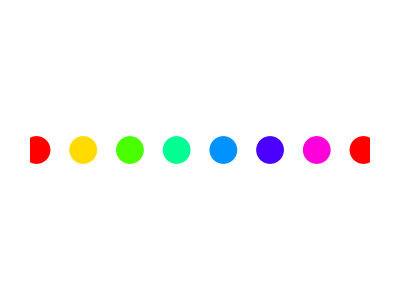

```mathematica
Graphics[{PointSize[.05],
Table[{Hue[i/7],Point[{i,0}]},{i,0,7}]
}]
```

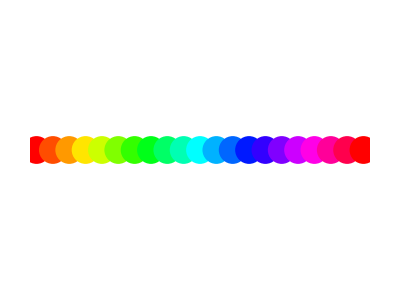

```mathematica
Graphics[{PointSize[.05],
Table[{Hue[i/20],Point[{i,0}]},{i,0,20}]
}]
```

We can also change how transparent the shape is using the Opacity command.

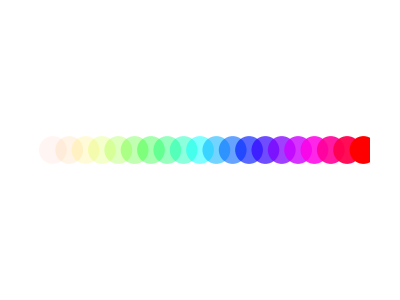

```mathematica
Graphics[{PointSize[.05],
Table[{Hue[i/20],Opacity[i/20],Point[{i,0}]},{i,0,20}]
}]
```

## 8.5. 1D objects: Line segments

To create line segments, use the Line command.  The input is a list of coordinates of initial, intermediate, and terminal vertices of the sequence of line segments you wish to display.
Remember that all graphics objects need to be included in a Graphics command to be displayed.

```mathematica
Line[{{0,0},{1,1}}]
```

Line[{{0,0},{1,1}}]

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

-Graphics-

A sequence of line segments creates a path.  If you connect the points {{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}},

```mathematica
Graphics[Map[Point,{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}]]
```

-Graphics-

It gives a zigzag pattern:

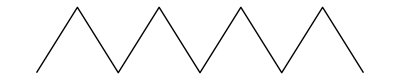

```mathematica
Graphics[Line[{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}]]
```

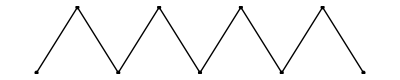

```mathematica
Graphics[{
Map[Point,{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}],
Line[{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}]
}]
```

By default, the line segments are displayed without axes or identifying markers.  So if you display the line segment from (0,0) to (1,1) it looks the same as the segment from (1,0) to (2,1).

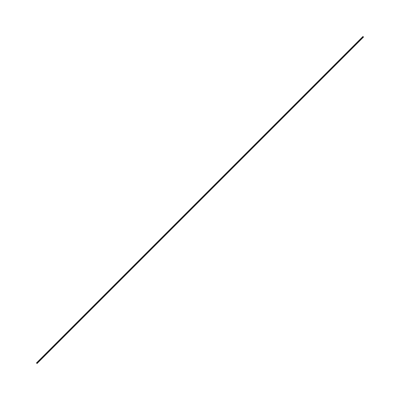
{-Graphics-,-Graphics-}

```mathematica
{Graphics[Line[{{0,0},{1,1}}]],Graphics[Line[{{1,0},{2,1}}]]}
```

## 8.6. Display Options

To rectify that, use the PlotRange and Axes options.
Here is some code that will display a line segment in the window [-2,2]x[-2,2], displaying axes:

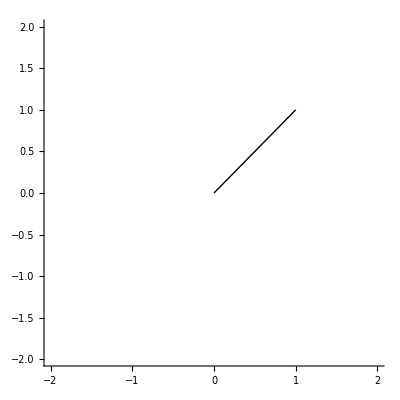
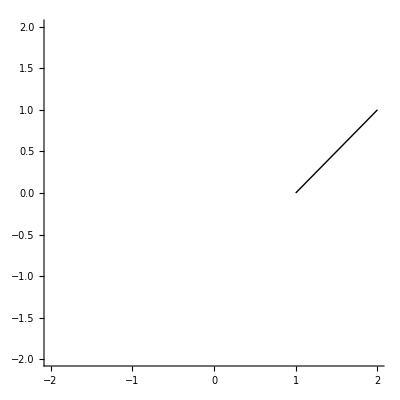

```mathematica
{Graphics[Line[{{0,0},{1,1}}],PlotRange->{{-2,2},{-2,2}},Axes->True],
Graphics[Line[{{1,0},{2,1}}],PlotRange->{{-2,2},{-2,2}},Axes->True]}
```

Also, if you are showing multiple graphics, you can use the PlotRange->All option to display all the graphics and not just inherit the bounds from the first argument of the Show command.  Compare the following.  In the first example, the combined graphic inherits the PlotRange option from the first argument, while the PlotRange->All ignores the individual PlotRange option from the first argument.

```mathematica
Graphics[Line[{{0,0},{1,1}}],PlotRange->{{0,1},{0,1}}]
```

-Graphics-

```mathematica
Show[{
Graphics[Line[{{0,0},{1,1}}],PlotRange->{{0,1},{0,1}}],
Graphics[Line[{{1,0},{2,1}}]]
}]
```

-Graphics-

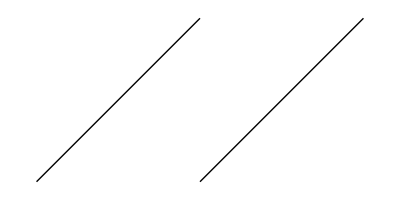

```mathematica
Show[{
Graphics[Line[{{0,0},{1,1}}],PlotRange->{{0,1},{0,1}}],
Graphics[Line[{{1,0},{2,1}}]]
},PlotRange->All]
```

Another option is ImageSize, in case you want to specify the size of your graphic.

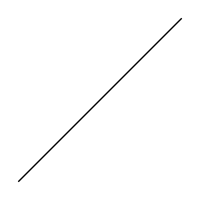
{-Graphics-,-Graphics-}

```mathematica
{Graphics[Line[{{0,0},{1,1}}],ImageSize->100],
Graphics[Line[{{0,0},{1,1}}],ImageSize->200]}
```

Do Now: Navigate to the Documentation Center entry for Line, and look at the “Neat Examples” at the bottom.

## 8.7. Circles

To display a point in space, you can use the Point command, but instead you probably use the Disk command, or its friend the Circle command, give filled in or empty circles (or ellipses, or parts thereof).

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

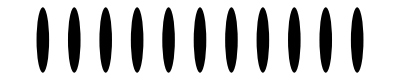

```mathematica
Graphics[Table[Disk[{i,0},.2],{i,0,10}]]
```

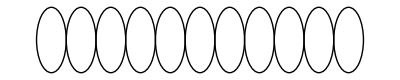

```mathematica
Graphics[Table[Circle[{i,0},.5],{i,0,10}]]
```

Note that we can also use a Map command here:

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

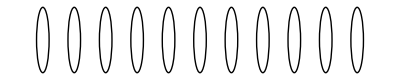

```mathematica
coords=Table[{i,0},{i,0,10}]
Graphics[Map[Circle[#,.2]&,coords]]
```

```mathematica
coords=RandomReal[{0,1},{10,2}]
```

{{0.219869,0.433304},{0.100254,0.865211},{0.399782,0.49232},{0.603689,0.627936},{0.540904,0.85517},{0.815354,0.487304},{0.982395,0.4082},{0.0756977,0.848224},{0.5689,0.675902},{0.862546,0.909748}}

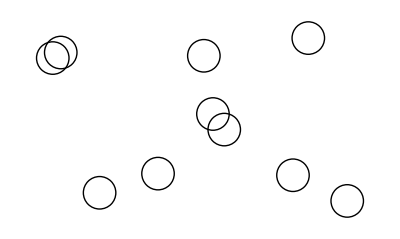

```mathematica
Graphics[Map[Circle[#,.05]&,coords]]
```

When you apply a color to a disk primitive, then it colors the whole object; if you want the boundary to be a different color, use the EdgeForm option:

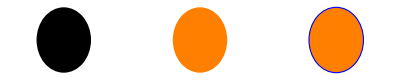

```mathematica
Graphics[{
{Disk[{0,0},.2]},
{Orange,Disk[{1,0},.2]},
{Orange,EdgeForm[{Blue,Thick,Dashed}],Disk[{2,0},.2]}
}]
```

Do Now: Navigate to the Documentation Center entry for Disk, and look at the “Neat Examples” at the bottom.

## 8.8. Polygons

A Line primitive can be used to give a closed unfilled polygon if the first and last coordinates are the same.
If you want to have a closed filled polygon, use the Polygon primitive.  (So Polygon is to Line as Disk is to Circle.)
You can see that while the Line must have the first and last coordinates the same, this is not necessary in Polygon.
And use EdgeForm just as in Disk.

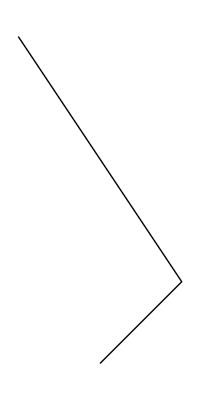
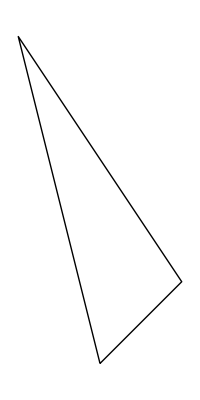
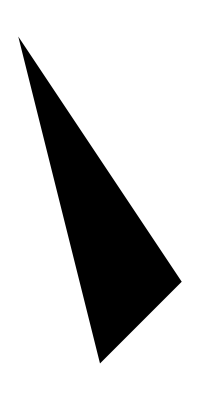
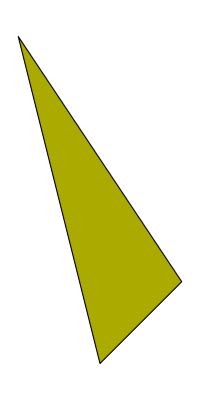

```mathematica
{
Graphics[Line[{{0,1},{1,2},{-1,5}}]],
Graphics[Line[{{0,1},{1,2},{-1,5},{0,1}}]],
Graphics[Polygon[{{0,1},{1,2},{-1,5}}]],
Graphics[{EdgeForm[{Black,Thin}],Darker[Yellow],Polygon[{{0,1},{1,2},{-1,5}}]}]
}
```

A regular n-gon is a polygon where each of the n edges are the same length and each of the n angles are the same.  Instead of guessing the coordinates for the vertices of a regular polygon, instead use Mathematica’s computing ability to calculate n equally spaced points on a circle.  Since there are n vertices to place on a circle with 2π radians, then place the vertices at coordinates (cos((2π i)/n),sin((2π i)/n)) as i ranges from 0 to n.  When n=5, we have the coordinates:

```mathematica
Range[0,2Pi,2Pi/5]
```

{0,(2 π)/5,(4 π)/5,(6 π)/5,(8 π)/5,2 π}

```mathematica
Map[{Cos[#],Sin[#]}&,%]
```

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{1,0}}

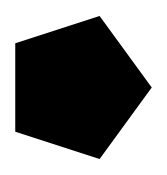

```mathematica
Graphics[Polygon[%]]
```

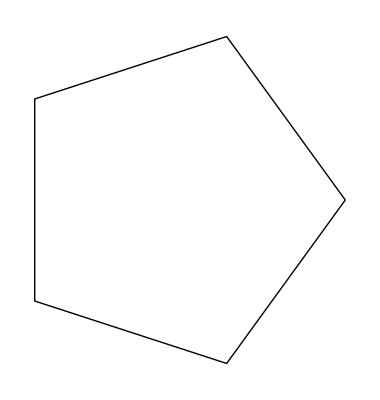

```mathematica
Graphics[Line[%%]]
```

1

{{1,0},{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)},{1,0}}

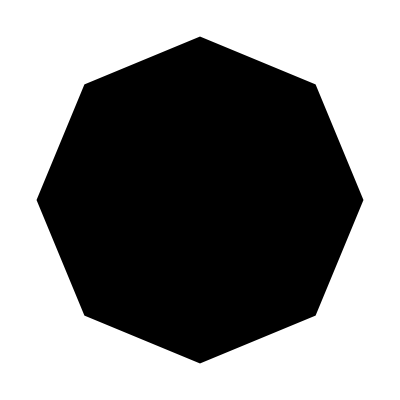

```mathematica
radius=1
ngon=Module[{n=8},Table[{radius*Cos[2Pi i/n],radius*Sin[2 Pi i/n]},{i,0,n}]]
Graphics[Polygon[ngon]]
```

Mathematica also already has these regular polygons built in:

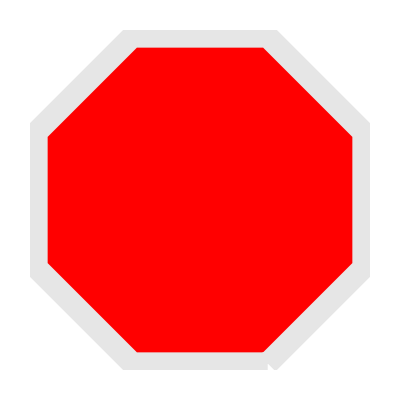

```mathematica
Graphics[{EdgeForm[{Thickness[.04],Darker[White,.1]}],Red,RegularPolygon[8]}]
```

Do Now: Navigate to the Documentation Center entry for Polygon, and look at the “Neat Examples” at the bottom.